# Aproximação Analítica

## Ordem Zero

Resolução da equação

```mathematica
r2=DSolve[{φ''[x]+2/x*φ'[x]-b*φ[x]/Sqrt[a]== -b}, φ[x],x]
```

{{φ[x]→√a+(ⅇ^(-(√b x)/a^(1/4)) C[1])/x+(a^(1/4) ⅇ^((√b x)/a^(1/4)) C[2])/(2 √b x)}}

Condição fronteira: (d Phi/dx | x = 0) = 0

```mathematica
{{φ[x]->√a+(ⅇ^(-(√b x)/a^(1/4)) C[1])/x+(a^(1/4) ⅇ^((√b x)/a^(1/4)) C[2])/(2 √b x)}}
D[√a+(ⅇ^(-(√b x)/a^(1/4)) C[1])/x+(a^(1/4) ⅇ^((√b x)/a^(1/4)) C[2])/(2 √b x), x]
```

{{φ[x]→√a+(ⅇ^(-(√b x)/a^(1/4)) C[1])/x+(a^(1/4) ⅇ^((√b x)/a^(1/4)) C[2])/(2 √b x)}}

-(ⅇ^(-(√b x)/a^(1/4)) C[1])/x^2-(√b ⅇ^(-(√b x)/a^(1/4)) C[1])/(a^(1/4) x)-(a^(1/4) ⅇ^((√b x)/a^(1/4)) C[2])/(2 √b x^2)+(ⅇ^((√b x)/a^(1/4)) C[2])/(2 x)

```mathematica
Limit[-(ⅇ^(-(√b x)/a^(1/4)) C[1])/x^2-(√b ⅇ^(-(√b x)/a^(1/4)) C[1])/(a^(1/4) x)-(a^(1/4) ⅇ^((√b x)/a^(1/4)) C[2])/(2 √b x^2)+(ⅇ^((√b x)/a^(1/4)) C[2])/(2 x), x->0]
```

DirectedInfinity[-2 C[1]-(a^(1/4) C[2])/(√b)]

```mathematica
c1 = -(a^(1/4) C[2])/(2*√b)
```

-(a^(1/4) C[2])/(2 √b)

```mathematica
φ[x]->√a-(a^(1/4) C[2])/(2*√b)(ⅇ^(-(√b x)/a^(1/4)))/x+(a^(1/4) ⅇ^((√b x)/a^(1/4)) C[2])/(2 √b x)
```

φ[x]→√a-(a^(1/4) ⅇ^(-(√b x)/a^(1/4)) C[2])/(2 √b x)+(a^(1/4) ⅇ^((√b x)/a^(1/4)) C[2])/(2 √b x)

```mathematica
φ[x]->√a+(a^(1/4) C[2])/(x*√b)((ⅇ^((√b x)/a^(1/4)))/2-(ⅇ^(-(√b x)/a^(1/4)))/2)
```

φ[x]→√a+(a^(1/4) (-1/2 ⅇ^(-(√b x)/a^(1/4))+1/2 ⅇ^((√b x)/a^(1/4))) C[2])/(√b x)

```mathematica
φ[x]->√a+(a^(1/4) * c2)/(x*√b)*Sinh [(√b x)/a^(1/4)]
```

φ[x]→√a+(a^(1/4) c2 Sinh[(√b x)/a^(1/4)])/(√b x)

Condição fronteira: phi(10) = 220

```mathematica
Solve[√a+(a^(1/4) * c2)/(10*√b)*Sinh [(√b* 10)/a^(1/4)]== 220, c2]
```

{{c2→-(10 (-220+√a) √b Csch[(10 √b)/a^(1/4)])/a^(1/4)}}

```mathematica
φ[x]->√a-(a^(1/4) *(10 (-220+√a) √b Csch[(10 √b)/a^(1/4)])/a^(1/4) *Sinh[(√b x)/a^(1/4)])/(√b x)
```

φ[x]→√a-(10 (-220+√a) Csch[(10 √b)/a^(1/4)] Sinh[(√b x)/a^(1/4)])/x

```mathematica
a = 10
```

10

```mathematica
Clear [a]
```

```mathematica
b=10
```

10

Solução da aproximação analítica de ordem zero

```mathematica
φ[x]->√10-(10^(1/4) *(10 (-220+√a) √10 Csch[(10 √10)/10^(1/4)])/10^(1/4) *Sinh[(√10 x)/10^(1/4)])/(√10 x)
```

φ[x]→√10-(10 (-220+√a) Csch[10 10^(1/4)] Sinh[10^(1/4) x])/x

```mathematica
Plot[φ[x], {x, 0.1, 10}]
```

-Graphics-

```mathematica
r =√10- Sinh[10^(1/4)*x]/x*Csch[10 10^(1/4)] *(10 *(-220+√10))
```

√10-(10 (-220+√10) Csch[10 10^(1/4)] Sinh[10^(1/4) x])/x

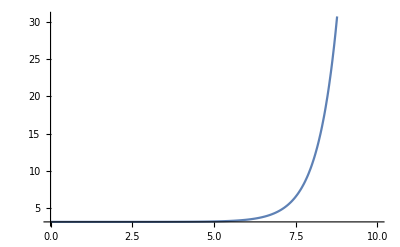

```mathematica
Plot[r, {x,0,10}]
```

## Ordem 1

Equação para chegar ao valor de ϕ que minimiza o potencial

```mathematica
r3=Solve[ϕ^2*(1+ϕ)-a==0, ϕ]
```

{{ϕ→1/3 (-1+2^(1/3)/((-2+27 a+3 √3 √(-4 a+27 a^2))^(1/3))+((-2+27 a+3 √3 √(-4 a+27 a^2))^(1/3))/2^(1/3))},{ϕ→-1/3-(1+ⅈ √3)/(3 2^(2/3) (-2+27 a+3 √3 √(-4 a+27 a^2))^(1/3))-((1-ⅈ √3) (-2+27 a+3 √3 √(-4 a+27 a^2))^(1/3))/(6 2^(1/3))},{ϕ→-1/3-(1-ⅈ √3)/(3 2^(2/3) (-2+27 a+3 √3 √(-4 a+27 a^2))^(1/3))-((1+ⅈ √3) (-2+27 a+3 √3 √(-4 a+27 a^2))^(1/3))/(6 2^(1/3))}}

```mathematica
FullSimplify[r3]
```

{{ϕ→1/3 (-1+1/(-1+(27 a)/2+3/2 √3 √(a (-4+27 a)))^(1/3)+(-1+(27 a)/2+3/2 √3 √(a (-4+27 a)))^(1/3))},{ϕ→1/6 (-2-(2 (-2)^(1/3))/(-2+27 a+3 √3 √(a (-4+27 a)))^(1/3)+(-2)^(2/3) (-2+27 a+3 √3 √(a (-4+27 a)))^(1/3))},{ϕ→1/6 (-2+(2 (-1)^(2/3))/(-1+(27 a)/2+3/2 √3 √(a (-4+27 a)))^(1/3)+(-2+27 a+3 √3 √(a (-4+27 a)))^(1/3) Root-0.794-1.37 ⅈRoot[-4+#1^3&,2]-0.7937005259840998)}}

```mathematica
Rc = 1
```

1

```mathematica
F= 1
```

1

```mathematica
1
```

1

```mathematica
phic=1
```

```mathematica
1
Clear[phic]
```

1

Resolução da equação

```mathematica
phim = (rhoc/rhoG)^(1/2)
```

√(rhoc/rhoG)

```mathematica
Clear[phim]
```

```mathematica
r4 =DSolve[{φ''[x]+2/x*φ'[x]-Rc^2 mc^2*phic^3*phim^3*φ[x]== -Rc^2 mc^2*phic^2*phim }, φ[x],x]
```

{{φ[x]→rhoG/(phic rhoc)+(ⅇ^(-(mc phic^(3/2) √rhoc (rhoc/rhoG)^(1/4) x)/(√rhoG)) C[1])/x+(ⅇ^((mc phic^(3/2) √rhoc (rhoc/rhoG)^(1/4) x)/(√rhoG)) C[2])/x}}

Condição fronteira : (d phi/dx | x=0 ) =0

```mathematica
D[1/(phic phim^2)+(ⅇ^(-mc phic^(3/2) phim^(3/2) Rc x) C[1])/x+(ⅇ^(mc phic^(3/2) phim^(3/2) Rc x) C[2])/(2 mc phic^(3/2) phim^(3/2) Rc x),x]
```

-(ⅇ^(-mc phic^(3/2) (rhoc/rhoG)^(3/4) x) C[1])/x^2-(ⅇ^(-mc phic^(3/2) (rhoc/rhoG)^(3/4) x) mc phic^(3/2) (rhoc/rhoG)^(3/4) C[1])/x-(ⅇ^(mc phic^(3/2) (rhoc/rhoG)^(3/4) x) C[2])/(2 mc phic^(3/2) (rhoc/rhoG)^(3/4) x^2)+(ⅇ^(mc phic^(3/2) (rhoc/rhoG)^(3/4) x) C[2])/(2 x)

```mathematica
Limit[-(ⅇ^(-mc phic^(3/2) (rhoc/rhoG)^(3/4) x) C[1])/x^2-(ⅇ^(-mc phic^(3/2) (rhoc/rhoG)^(3/4) x) mc phic^(3/2) (rhoc/rhoG)^(3/4) C[1])/x-(ⅇ^(mc phic^(3/2) (rhoc/rhoG)^(3/4) x) C[2])/(2 mc phic^(3/2) (rhoc/rhoG)^(3/4) x^2)+(ⅇ^(mc phic^(3/2) (rhoc/rhoG)^(3/4) x) C[2])/(2 x), x->0, GenerateConditions->False]
```

DirectedInfinity[-2 C[1]-C[2]/(mc phic^(3/2) (rhoc/rhoG)^(3/4))]

```mathematica
c1 = (-1/2)*c2/Sqrt[c]
```

-c2/(2 √c)

```mathematica
φ[x]->phim/phic-(ⅇ^(-√c x) c2/(2 √c))/x+(ⅇ^(√c x) C[2])/(2 √c x)
```

φ[x]→√(rhoc/rhoG)-(c2 ⅇ^(-√c x))/(2 √c x)+(ⅇ^(√c x) C[2])/(2 √c x)

Condição fronteira: phi(10) = 220

```mathematica
Solve[phim/phic-(ⅇ^(-√c *10) x/(2 √c))/10+(ⅇ^(√c 10) x)/(2 √c 10)==220, x]
```

{{x→-(20 √c ⅇ^(10 √c) (-220+√(rhoc/rhoG)))/(-1+ⅇ^(20 √c))}}

Solução da aproximação de primeira ordem

```mathematica
φ[x]->phim/phic+(20 √c ⅇ^(10 √c) (220 phic-phim))/((-1+ⅇ^(20 √c)) phic)*1/(Sqrt[c]*x)*Sinh[Sqrt[c]*x]/2
```

φ[x]→√(rhoc/rhoG)+(10 ⅇ^(10 √c) (220-√(rhoc/rhoG)) Sinh[√c x])/((-1+ⅇ^(20 √c)) x)

```mathematica
φ[x]->phim/phic+(10 ⅇ^(10 √c) (220 phic-phim) Sinh[√c x])/((-1+ⅇ^(20 √c)) phic x)
```

φ[x]→√(rhoc/rhoG)+(10 ⅇ^(10 √c) (220-√(rhoc/rhoG)) Sinh[√c x])/((-1+ⅇ^(20 √c)) x)

1+(2190 ⅇ^(10 √2) Sinh[x])/((-1+ⅇ^(20 √2)) x)

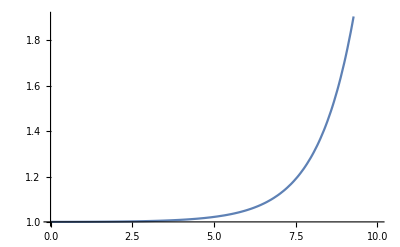

```mathematica
r5=1+(2190 ⅇ^(10 √2) Sinh[x])/((-1+ⅇ^(20 √2)) x)
Plot[r5, {x,0,10}]
```